Writing Good Code

Writing good code is in many ways like writing good prose: you need to have your thoughts clear, and express them well. When you first start writing code, you’ll most likely think about what your code does in English or whatever natural language you use. But as you become fluent in the Wolfram Language you’ll start thinking directly in code, and it’ll be faster for you to type a program than to describe what it does.

My goal as a language designer has been to make it as easy as possible to express things in the Wolfram Language. The functions in the Wolfram Language are much like the words in a natural language, and I’ve worked hard to choose them well.

Functions like Table or NestList or FoldList exist in the Wolfram Language because they express common things one wants to do. As in natural language, there are always many ways one can in principle express something. But good code involves finding the most direct and simple way.

To create a table of the first 10 squares in the Wolfram Language, there’s an obvious good piece of code that just uses the function Table.

Simple and good Wolfram Language code for making a table of the first 10 squares:

```mathematica
Table[n^2,{n,10}]
```

{1,4,9,16,25,36,49,64,81,100}

Why would anyone write anything else? A common issue is not thinking about the “whole table”, but instead thinking about the steps in building it. In the early days of computing, computers needed all the help they could get, and there was no choice but to give code that described every step to take.

A much worse piece of code that builds up the table step by step:

```mathematica
Module[{list,i}, list={}; For[i=1,i≤10,i++, list=Append[list,i^2]];list]
```

{1,4,9,16,25,36,49,64,81,100}

But the point of the Wolfram Language is to let one express things at a higher level—and to create code that as directly as possible captures the concept of what one wants to do. Once one knows the language, it’s vastly more efficient to operate at this level. And it leads to code that’s easier for both computers and humans to understand.

In writing good code, it’s important to ask frequently, “What’s the big picture of what this code is trying to do?” Often you’ll start off understanding only some part, and writing code just for that. But then you’ll end up extending it, and adding more and more pieces to your code. But if you think about the big picture you may suddenly realize that there’s some more powerful function—like a Fold—that you can use to make your code nice and simple again.

Make code to convert {hundreds,tens,ones} digits to a single integer:

```mathematica
fromdigits[{h_,t_,o_}]:=100h+10t+o
```

Run the code:

```mathematica
fromdigits[{5,6,1}]
```

561

Write a generalization to a list of any length, using Table:

```mathematica
fromdigits[list_List]:=Total[Table[10^(Length[list]-i)*list[[i]],{i,Length[list]}]]
```

The new code works:

```mathematica
fromdigits[{5,6,1,7,8}]
```

56178

Simplify the code by multiplying the whole list of powers of 10 at the same time:

```mathematica
fromdigits[list_List]:=Total[10^Reverse[Range[Length[list]]-1]*list]
```

Try a different, recursive, approach, after first clearing the earlier definitions:

```mathematica
Clear[fromdigits]
```

```mathematica
fromdigits[{k_}]:=k
```

```mathematica
fromdigits[{digits___,k_}]:=10*fromdigits[{digits}]+k
```

The new approach works too:

```mathematica
fromdigits[{5,6,1,7,8}]
```

56178

But then you realize: it’s actually all just a Fold!

```mathematica
Clear[fromdigits]
```

```mathematica
fromdigits[list_]:=Fold[10*#1+#2&,list]
```

```mathematica
fromdigits[{5,6,1,7,8}]
```

56178

Of course, there’s a built-in function that does it too:

```mathematica
FromDigits[{5,6,1,7,8}]
```

56178

Why is it good for code to be simple? First, because it’s more likely to be correct. It’s much easier for a mistake to hide in a complicated piece of code than a simple one. Code that’s simple is also usually more general, so it’ll tend to cover even cases you didn’t think of, and avoid you having to write more code. And finally, simple code tends to be much easier to read and understand. (Simpler isn’t always the same as shorter, and in fact short “code poetry” can get hard to understand.)

An overly short version of fromdigits, that’s starting to be difficult to understand:

```mathematica
fromdigits =Fold[{10,1}.{##}&,#]& ;
```

It still works though:

```mathematica
fromdigits[{5,6,1,7,8}]
```

56178

If what you’re trying to do is complicated, then your code may inevitably need to be complicated. Good code, though, is broken up into functions and definitions that are each as simple and self-contained as possible. Even in very large Wolfram Language programs, there may be no individual definitions longer than a handful of lines.

Here’s a single definition that combines several cases:

```mathematica
fib[n_]:=If[!IntegerQ[n]||n<1,"Error",If[n==1||n==2,1,fib[n-1]+fib[n-2]]]
```

It’s much better to break it up into several simpler definitions:

```mathematica
fib[1]=fib[2]=1;
```

```mathematica
fib[n_Integer]:=fib[n-1]+fib[n-2]
```

A very important aspect of writing good code is choosing good names for your functions. For the built-in functions of the Wolfram Language, I’ve made a tremendous effort over the course of decades to pick names well—and to capture in their short names the essence of what the functions do, and how to think about them.

When you’re writing code, it’s common to first define a new function because you need it in some very specific context. But it’s almost always worth trying to give it a name that you’ll understand even outside that context. And if you can’t find a good name, it’s often a sign that it’s not quite the right function to define in the first place.

A sign of a good function name is that when you read it in a piece of code, you immediately know what the code does. And indeed, it’s an important feature of the Wolfram Language that it’s typically easier to read and understand well-written code directly than from any kind of textual description of it.

How would one describe this in plain English?

```mathematica
Graphics[{White,Riffle[NestList[Scale[Rotate[#,0.1],0.9]&,Rectangle[ ],40],{Pink,Yellow}]}]
```

-Graphics-

When you write Wolfram Language code, you’ll sometimes have to choose between using a single rare built-in function that happens to do exactly what you want—and building up the same functionality from several more common functions. In this book, I’ve sometimes chosen to avoid rare functions so as to minimize vocabulary. But the best code tends to use single functions whenever it can—because the name of the function explains the intent of the code in a way that individual pieces cannot.

Use a small piece of code to reverse the digits in an integer:

```mathematica
FromDigits[Reverse[IntegerDigits[123456]]]
```

654321

Using a single built-in function explains the intent more clearly:

```mathematica
IntegerReverse[123456]
```

654321

Good code needs to be correct and easy to understand. But it also needs to run efficiently. And in the Wolfram Language, simpler code is typically better here too—because by explaining your intent more clearly, it makes it easier for the Wolfram Language to optimize how the computations you need are done internally.

With every new version, the Wolfram Language does better at automatically figuring out how to make your code run fast. But you can always help by structuring your algorithms well.

Timing gives the timing of a computation (in seconds), together with its result:

```mathematica
Timing[fib[20]]
```

{0.021843,6765}

Plot the time to compute fib[n] according to the definitions above.

With the definitions of fib above, the time grows very rapidly:

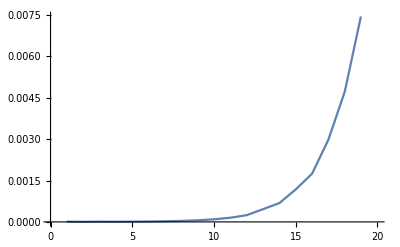

```mathematica
ListLinePlot[Table[First[Timing[fib[n]]],{n,20}]]
```

The algorithm we used happens to do an exponential amount of unnecessary work recomputing what it’s already computed before. We can avoid this by making the definition for fib[n_] always do an assignment for fib[n], so it stores the result of each intermediate computation.

Redefine the fib function to remember every value it computes:

```mathematica
fib[1]=fib[2]=1;
```

```mathematica
fib[n_Integer]:=fib[n]=fib[n-1]+fib[n-2]
```

Now even up to 1000 each new value takes only microseconds to compute:

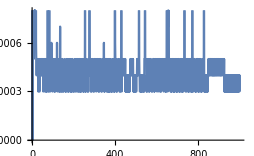

```mathematica
ListLinePlot[Table[First[Timing[fib[n]]],{n,1000}]]
```

Vocabulary

FromDigits[list] |   | assemble an integer from its digits
IntegerReverse[n] |   | reverse the digits in an integer
Timing[expr] |   | do a computation, timing how long it takes

"5 Exercises Available" | "Get Started »"

Find a simpler form for Module[{a,i},a=0; For[i=1,i≤1000,i++,a=i*(i+1)+a];a]. »

| Expected output: |  
  | 334334000 |

Find a simpler form for Module[{a,i},a=x; For[i=1,i≤10,i++, a=1/(1+a)];a]. »

| Expected output: |  
  | 1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+x)))))))))) |

Find a simpler form for Module[{i,j,a},a={}; For[i=1,i≤10,i++,For[j=1,j≤10,j++,a=Join[a,{i,j}]]];a]. »

| Expected output: |  
  | {1,1,1,2,1,3,1,4,1,5,1,6,1,7,1,8,1,9,1,10,2,1,2,2,2,3,2,4,2,5,2,6,2,7,2,8,2,9,2,10,3,1,3,2,3,3,3,4,3,5,3,6,3,7,3,8,3,9,3,10,4,1,4,2,4,3,4,4,4,5,4,6,4,7,4,8,4,9,4,10,5,1,5,2,5,3,5,4,5,5,5,6,5,7,5,8,5,9,5,10,6,1,6,2,6,3,6,4,6,5,6,6,6,7,6,8,6,9,6,10,7,1,7,2,7,3,7,4,7,5,7,6,7,7,7,8,7,9,7,10,8,1,8,2,8,3,8,4,8,5,8,6,8,7,8,8,8,9,8,10,9,1,9,2,9,3,9,4,9,5,9,6,9,7,9,8,9,9,9,10,10,1,10,2,10,3,10,4,10,5,10,6,10,7,10,8,10,9,10,10} |

Make a line plot of the timing for computing n^n for n up to 10000. »

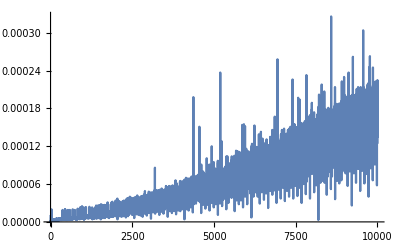
| Expected output: |  
  | -Graphics- |

Make a line plot of the timing for Sort to sort Range[n] from a random order, for n up to 200. »

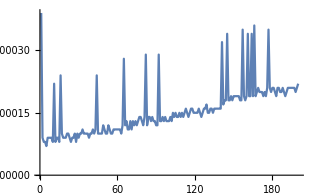
| Sample expected output: |  
  | -Graphics- |

Q&A

What does i++ mean?

It’s a short notation for i=i+1. It’s the same notation that C and many other low-level computer languages use for this increment operation.

What does the For function do?

It’s a direct analog of the for(...) statement in C. For[start,test,step,body] first executes start, then checks test, then executes step, then body. It does this repeatedly until test no longer gives True.

Why can shortened pieces of code be hard to understand?

The most common issue is that variables and sometimes even functions have been factored out, so there are fewer names to read that might give clues about what the code is supposed to do.

What’s the best IDE for authoring Wolfram Language code?

For everyday programming, Wolfram Notebooks are best. Make sure to add sections, text and examples right alongside your code. For large multi-developer software projects, Wolfram Workbench provides an Eclipse-based IDE.

What does Timing actually measure?

It measures the CPU time spent in the Wolfram Language actually computing your result. It doesn’t include time to display the result. Nor does it include time spent on external operations, like fetching data from the cloud. If you want the absolute “wall clock” time, use AbsoluteTiming.

How can I get more accurate timings for code that runs fast?

Use RepeatedTiming, which runs code many times and averages the timings it gets. (This won’t work if the code is modifying itself, like in the last definition of fib above.)

What are some tricks for speeding up code?

Beyond keeping the code simple, one thing is not to recompute anything you don’t have to. Also, if you’re dealing with lots of numbers,  it may make sense to use N to force the numbers to be approximate. For some internal algorithms you can pick your PerformanceGoal, typically trading off speed and accuracy. There are also functions like Compile that force more of the work associated with optimization to be done up front, rather than during a computation.

Tech Notes

Complicated behavior can arise even from extremely simple code: that’s what my 1280-page book A New Kind of Science is about. A good example is CellularAutomaton[30,{{1},0}].

The fib function is computing Fibonacci[n]. The original definition always recurses down a whole tree of O(ϕ^n) values, where ϕ≈1.618 is the golden ratio (GoldenRatio).

Remembering values that a function has computed before is sometimes called memoization, sometimes dynamic programming and sometimes just caching.

The function IntegerReverse was new in Version 10.3.

For large programs, the Wolfram Language has a framework for isolating functions into contexts and packages.

If[#1>2,2#0[#1-#0[#1-2]],1]&/@Range[50] is an example of short code that’s seriously challenging to understand...